The following notebook demonstrates the use of recurrence plots in determining if and when multimode forcing characteristics are damped out in a non-linear damped oscillator of the form x’’ + δ x’ + x + c x^3 + q x^2.  The value of q is maintained as 0.0 and c is 0.1.  This is a candidate for Poincare-Lindstedt method.  For now, the qualitative results and trends obnserved here will be extrapolated to analyse the fourth order film evolution equation with and without a porous substrate.

```mathematica
Needs["HierarchicalClustering`"]
SetOptions[{Plot,MatrixPlot},ImageSize->250{1,1}];
{tmax=200,δ=0.05,c=0.1,q=1.}
```

{200,0.05,0.1,1.}

An experiment on simple harmonic motion with a multimode forcing function vs a non-linear oscillator with the same multimode forcing function.

InterpolatingFunction[{{0., 200.}}, <>]

InterpolatingFunction[{{0., 200.}}, <>]

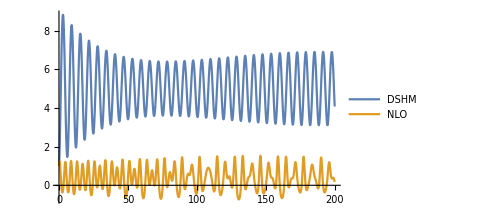

```mathematica
shm=NDSolveValue[{x''[t]+x[t]+0.05 x'[t]==5+0.1Sin[t/100]Sin[t],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"]
nlo=NDSolveValue[{x''[t]+x[t]+0.01 x'[t]+0.5(x[t])^3+(x[t])^2==1+Sin[t/100]Sin[t],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"]
Plot[{(*Cos[t]+Sin[t],*)shm[t],nlo[t]},{t,0,tmax},PlotLegends->{"DSHM","NLO"},ImageSize->Medium]
```

An undamped and a damped oscillator’s recurrence plots are compared.  No forcing function is used.

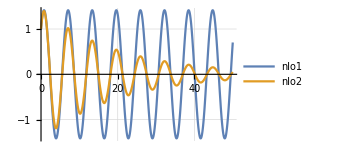
-Graphics- -Graphics- -Graphics-

```mathematica
Module[{tmax=50,δ,c=0.,q=0,x,t,nlo1,nlo2},
δ=0.0;nlo1=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==0,x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
δ=0.1;nlo2=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==0,x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
Plot[{nlo1[t],nlo2[t]},{t,0,tmax},GridLines->Automatic,PlotLegends->{"nlo1","nlo2"}]
With[{stepSize=0.1,end=tmax,nn=0.1},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]]]
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]]
```

An undamped oscillator’s recurrence plot is compared with that of an unstable oscillator

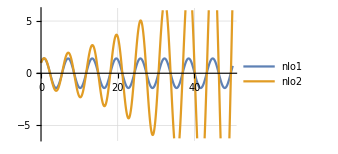
-Graphics- -Graphics- -Graphics-

```mathematica
Module[{tmax=50,δ,c=0.,q=0,x,t,nlo1,nlo2},
δ=0.;nlo1=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==0,x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
δ=-0.1;nlo2=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==0,x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
Plot[{nlo1[t],nlo2[t]},{t,0,tmax},GridLines->Automatic,PlotLegends->{"nlo1","nlo2"}]
With[{stepSize=.1,end=tmax,nn=0.1},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]]]
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]]
```

An undamped and a damped oscillator are compared. A single mode forcing function is used. The recurrence plot shows nearly similar characteristic. The undamped oscillator grows as a result of the forcing function.

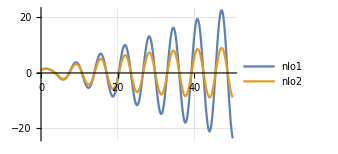
-Graphics- -Graphics- -Graphics-

```mathematica
Module[{tmax=50,δ,c=0.,q=0,x,t,nlo1,nlo2},
δ=0.;nlo1=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==Sin[t],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
δ=0.1;nlo2=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==Sin[t],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
Plot[{nlo1[t],nlo2[t]},{t,0,tmax},GridLines->Automatic,PlotLegends->{"nlo1","nlo2"}]
With[{stepSize=.1,end=tmax,nn=0.1},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]]]
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]]
```

Again, an undamped oscillator and damped oscillators with a multimode forcing function are compared through recurrence plots.

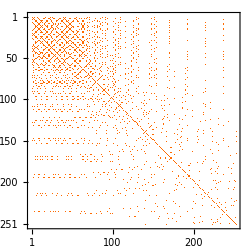
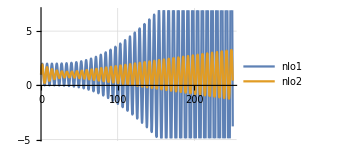
-Graphics- -Graphics- -Graphics-

```mathematica
Module[{tmax=250,δ,c=0.,q=0,x,t,nlo1,nlo2},
δ=0.;nlo1=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==1+Sin[t/1000]Sin[t],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
δ=0.1;nlo2=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==1+Sin[t/1000]Sin[t],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
Plot[{nlo1[t],nlo2[t]},{t,0,tmax},GridLines->Automatic,PlotLegends->{"nlo1","nlo2"}]
With[{stepSize=1,end=tmax,nn=0.1},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]]]
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]]
```

Non linear versions of the undamped and damped oscillators without a forcing function are compared.  x’’ + x + δ x’ + c x^3 + q x^2=0 with small q. The non-linear damped oscillator has its amplituded completely damped. At q=0.5, the equation becomes stiff with c=0.

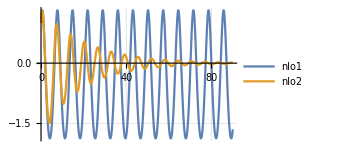
-Graphics- -Graphics- -Graphics-

```mathematica
Module[{tmax=90,δ,c=0.,q=0.1,x,t,nlo1,nlo2},
δ=0.;nlo1=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==0,x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
δ=0.1;nlo2=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==0,x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
Plot[{nlo1[t],nlo2[t]},{t,0,tmax},GridLines->Automatic,PlotLegends->{"nlo1","nlo2"}]
With[{stepSize=0.2,end=tmax,nn=0.1},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]]]
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]]
```

The non-linear undamped and damped oscillators with q=0.1 are now compared with a multimode forcing function. Multimode characteristics are seen for long times (t->100 or more).  With tmax ≈500, stiffness sets in.  The following code, with c=0, q=0.1, should be run for tmax=200.

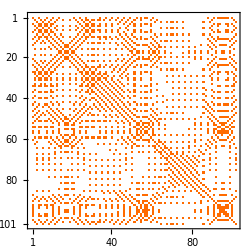
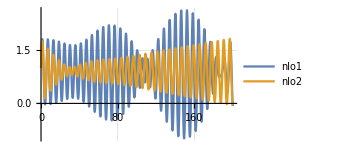
-Graphics- -Graphics- -Graphics-

```mathematica
Module[{tmax=200,δ,c=0.,q=0.1,x,t,nlo1,nlo2},
δ=0.;nlo1=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==1+Sin[t/1000]Sin[t/1],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
δ=0.1;nlo2=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==1+Sin[t/1000]Sin[t/1],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
Plot[{nlo1[t],nlo2[t]},{t,0,tmax},GridLines->Automatic,PlotLegends->{"nlo1","nlo2"}]
With[{stepSize=2,end=tmax,nn=0.1},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]]]
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]]
```

A larger value of δ damps the mixed modes at an earlier time period.

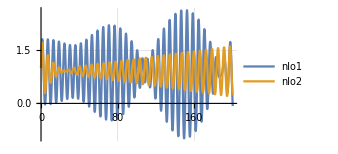
-Graphics- -Graphics- -Graphics-

```mathematica
Module[{tmax=200,δ,c=0.,q=.1,x,t,nlo1,nlo2},
δ=0.0;nlo1=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==1+Sin[t/1000]Sin[t/1],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
δ=0.2;nlo2=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==1+Sin[t/1000]Sin[t/1],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];
Plot[{nlo1[t],nlo2[t]},{t,0,tmax},GridLines->Automatic,PlotLegends->{"nlo1","nlo2"}]
With[{stepSize=2,end=tmax,nn=0.1},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]]]
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]]
```